```mathematica
(* Filename: Plot_example_in_experiment_3_b.nb *)
(* Ver. 0 (25-Apr-2023) *)
(*
This file is a program code in Mathematica to get plots in numerical experinemt 3.
*)
```

```mathematica
nn=127;
```

```mathematica
(***** In the following line, you need to set a path 
to the folder "experiment_3". *****)
datadir= "D:/.../experiment_3";
```

```mathematica
mydirB7 = StringJoin[datadir,"/By_wo2_srock2_Ab_values/dt=1_512/St7_Se1_Tr1000_B1"];
```

```mathematica
numSet=1;
fdim=2;
```

```mathematica
xPointList=Table[N[ii/(nn+1)],{ii,1,nn}];
yPointList=Table[N[jj/(nn+1)],{jj,1,nn}];
```

```mathematica
dataExB7=Table[{},{ii,1,fdim}];
dataProfileExB7=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataExB7[[ii]]=Table[{},{ii,1,nn^2}];
dataProfileExB7[[ii]]=Table[{},{ii,1,nn}];
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirB7<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
For[jj=1,jj<=nn,jj++,
dataExB7[[ii]][[nn*(kk-1)+jj]]={xPointList[[jj]],yPointList[[kk]],locTmp[[kk,jj]]};
];
];
kk=1;
For[jj=1,jj<=nn,jj++,
dataProfileExB7[[ii]][[nn*(kk-1)+jj]]={xPointList[[jj]],locTmp[[kk,jj]]};
];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirB7<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
For[jj=1,jj<=nn,jj++,
dataExB7[[ii]][[nn*(kk-1)+jj]][[3]]+=locTmp[[kk,jj]];
];
];
kk=1;
For[jj=1,jj<=nn,jj++,
dataProfileExB7[[ii]][[nn*(kk-1)+jj]][[2]]+=locTmp[[kk,jj]];
];
];
For[kk=1,kk<=nn,kk++,
For[jj=1,jj<=nn,jj++,
dataExB7[[ii]][[nn*(kk-1)+jj]][[3]]/=numSet;
];
];
kk=1;
For[jj=1,jj<=nn,jj++,
dataProfileExB7[[ii]][[nn*(kk-1)+jj]][[2]]/=numSet;
];
];
```

```mathematica
xMin=0;
xMax=1;
yMin=0;
yMax=1;
(***)
NumMesh=64; 
ll=0.02;
```

```mathematica
zExMin=Table[{},{ii,1,fdim}];
zExMax=Table[{},{ii,1,fdim}];
```

```mathematica
ii=1;
zExMin[[ii]]=0;
zExMax[[ii]]=0.4;
(***)
ii=2;
zExMin[[ii]]=0;
zExMax[[ii]]=0.4;
```

```mathematica
tmpPlotExpB7=Table[{},{ii,1,fdim}];
(***)
ii=1;
tmpPlotExpB7[[ii]]=ListPlot3D[dataExB7[[ii]],PlotRange->{{xMin,xMax},{yMin,yMax},{zExMin[[ii]],zExMax[[ii]]}},Mesh->NumMesh,Ticks->{Union[Table[{ii,ToString[ii],ll},{ii,0,1}],Table[{0.25ii,"",ll},{ii,0,10}]],Union[Table[{ii,ToString[ii],ll},{ii,0,1}],Table[{0.25ii,"",ll},{ii,0,10}]],Union[Table[{0.2ii,ToString[0.2ii],ll},{ii,1,10}],{{0,"0",ll}},Table[{ii,"",ll/2},{ii,0,10}]]},BaseStyle->{14,FontFamily->"Helvetica"}]
```

-Graphics3D-

```mathematica
dataOtherProfileExB7=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataOtherProfileExB7[[ii]]=Table[{},{ii,1,nn}];
basename[ii]=StringJoin["/expectfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirB7<>filename[ii],"Table"];
kk=64; (* 1, 32, 64 *)
For[jj=1,jj<=nn,jj++,
dataOtherProfileExB7[[ii]][[jj]]={xPointList[[jj]],locTmp[[kk,jj]]};
];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirB7<>filename[ii],"Table"];
For[jj=1,jj<=nn,jj++,
dataOtherProfileExB7[[ii]][[jj]][[2]]+=locTmp[[kk,jj]];
];
];
For[jj=1,jj<=nn,jj++,
dataOtherProfileExB7[[ii]][[jj]][[2]]/=numSet;
];
];
```

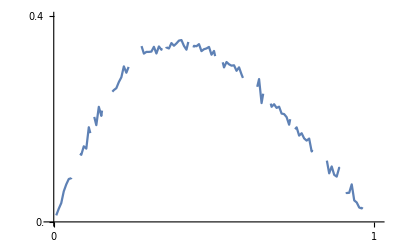

```mathematica
tmpPlotOtherProfileExB7=Table[{},{ii,1,fdim}];
epsilon=0.01;
(***)
ii=1;
tmpPlotOtherProfileExB7[[ii]]=ListPlot[dataOtherProfileExB7[[ii]],PlotRange->{{xMin-epsilon,xMax+epsilon},{zExMin[[ii]],zExMax[[ii]]}},Joined->True,Ticks->{Union[Table[{ii,ToString[ii],ll},{ii,0,1}],Table[{0.25ii,"",ll},{ii,0,10}]],Union[Table[{0.2ii,ToString[0.2ii],ll},{ii,0,10}],Table[{0.1ii,"",ll/2},{ii,0,10}]]},BaseStyle->{12,FontFamily->"Helvetica"},PlotStyle->{(*Thickness[tmpThickness],*)Dashing[{0.075,0.05}]}]
```

```mathematica
data2MomB7=Table[{},{ii,1,fdim}];
dataProfile2MomB7=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
data2MomB7[[ii]]=Table[1,{ii,1,nn^2}];
dataProfile2MomB7[[ii]]=Table[1,{ii,1,nn}];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirB7<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
For[jj=1,jj<=nn,jj++,
data2MomB7[[ii]][[nn*(kk-1)+jj]]={xPointList[[jj]],yPointList[[kk]],locTmp[[kk,jj]]};
];
];
kk=1;
For[jj=1,jj<=nn,jj++,
dataProfile2MomB7[[ii]][[nn*(kk-1)+jj]]={xPointList[[jj]],locTmp[[kk,jj]]};
];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirB7<>filename[ii],"Table"];
For[kk=1,kk<=nn,kk++,
For[jj=1,jj<=nn,jj++,
data2MomB7[[ii]][[nn*(kk-1)+jj]][[3]]+=locTmp[[kk,jj]];
];
];
kk=1;
For[jj=1,jj<=nn,jj++,
dataProfile2MomB7[[ii]][[nn*(kk-1)+jj]][[2]]+=locTmp[[kk,jj]];
];
];
For[kk=1,kk<=nn,kk++,
For[jj=1,jj<=nn,jj++,
data2MomB7[[ii]][[nn*(kk-1)+jj]][[3]]/=numSet;
];
];
kk=1;
For[jj=1,jj<=nn,jj++,
dataProfile2MomB7[[ii]][[nn*(kk-1)+jj]][[2]]/=numSet;
];
];
```

```mathematica
zMomMin=Table[{},{ii,1,fdim}];
zMomMax=Table[{},{ii,1,fdim}];
```

```mathematica
ii=1;
zMomMin[[ii]]=0;
zMomMax[[ii]]=0.3; 
(***)
ii=2;
zMomMin[[ii]]=0;
zMomMax[[ii]]=0.2;
```

```mathematica
dataOtherProfile2MomB7=Table[{},{ii,1,fdim}];
For[ii=1, ii≤fdim, ii++,
dataOtherProfile2MomB7[[ii]]=Table[1,{ii,1,nn}];
basename[ii]=StringJoin["/2momentfile",ToString[ii-1]];
filename[ii]=StringJoin["/Set_",ToString[1],basename[ii]];
locTmp=Import[mydirB7<>filename[ii],"Table"];
kk=64;
For[jj=1,jj<=nn,jj++,
dataOtherProfile2MomB7[[ii]][[jj]]={xPointList[[jj]],locTmp[[kk,jj]]};
];
For[iiset = 2,iiset≤numSet,iiset++,
filename[ii]=StringJoin["/Set_",ToString[iiset],basename[ii]];
locTmp=Import[mydirB7<>filename[ii],"Table"];
For[jj=1,jj<=nn,jj++,
dataOtherProfile2MomB7[[ii]][[jj]][[2]]+=locTmp[[kk,jj]];
];
];
For[jj=1,jj<=nn,jj++,
dataOtherProfile2MomB7[[ii]][[jj]][[2]]/=numSet;
];
];
```

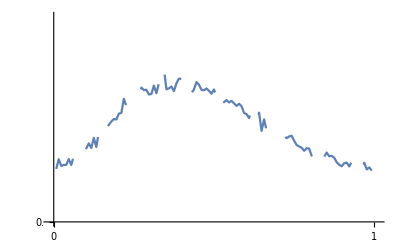

```mathematica
tmpPlotOtherProfile2MomB7=Table[{},{ii,1,fdim}];
epsilon=0.01;
(***)
ii=1;
tmpPlotOtherProfile2MomB7[[ii]]=ListPlot[dataOtherProfile2MomB7[[ii]],PlotRange->{{xMin-epsilon,xMax+epsilon},{zMomMin[[ii]],zMomMax[[ii]]}},Joined->True,Ticks->{Union[Table[{ii,ToString[ii],ll},{ii,0,1}],Table[{0.25ii,"",ll},{ii,0,10}]],Union[Table[{0.2ii,ToString[0.2ii],ll},{ii,0,10}],Table[{0.1ii,"",ll/2},{ii,0,10}]]},BaseStyle->{12,FontFamily->"Helvetica"},PlotStyle->{Dashing[{0.075,0.05}]}]
```